```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[1/2 ((2 π)/3-2 γb)] Cos[2 γb]-rb Sin[1/2 ((2 π)/3-2 γb)] Sin[2 γb],rb Cos[2 γb] Sin[1/2 ((2 π)/3-2 γb)]+rb Cos[1/2 ((2 π)/3-2 γb)] Sin[2 γb],0}

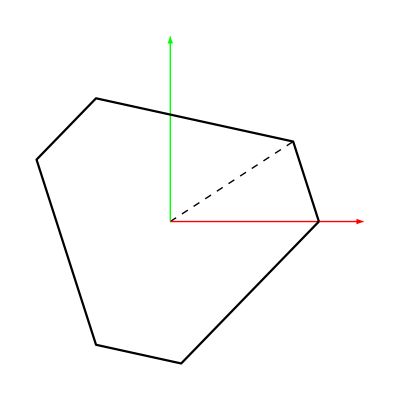

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

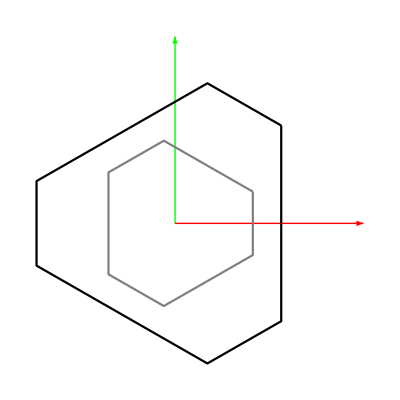

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}];(*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksol[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, q/.qrule, iksol[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]]
```

1.77636×10^-15

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
```

```mathematica
qfull = Join[qx, qvar];
```

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
index = 2;
initpose = Join[qx/.roots[[index]], iksol[qx/.roots[[index]]]];
plotsrspm[Inner[Rule, qfull, initpose, List]]
```

-Graphics3D-

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.8],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, axis]
]
```

```mathematica
plotsrspm[Inner[Rule, qfull, initpose, List]]
```

-Graphics3D-

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

```mathematica
scale = 0.2;
parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]};
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
iksol[pathpts[[1]]][[-6;;]]
```

{1.44582,1.56868,1.57865,1.33939,1.15248,1.28688}

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksol[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[pathpts[[;;u]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksol[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
Inner[List, q/.qrule, Table[_Real, {i, Length[q]}], List]
```

{{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}

```mathematica
cηconfig =  Compile[{{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
initpose[[7;;]]
cηconfig@@initpose[[7;;]]
```

{0.00305624,-0.0668855,0.456963,0.546956,-0.0946901,0.00349011,0.336276,0.286891,-0.0210274,0.0247844,-0.395383,-0.379795,1.44582,1.56868,1.57865,1.33939,1.15248,1.28688}

{1.05471×10^-15,0.,3.90313×10^-17,0.,7.21645×10^-16,0.,-4.44089×10^-16,0.,8.88178×10^-16,3.19189×10^-16,-1.11022×10^-16,-8.32667×10^-17}

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
initpose[[7;;]]
```

{0.00305624,-0.0668855,0.456963,0.546956,-0.0946901,0.00349011,0.336276,0.286891,-0.0210274,0.0247844,-0.395383,-0.379795,1.44582,1.56868,1.57865,1.33939,1.15248,1.28688}

```mathematica
testconfig = initpose[[7;;-7]];
```

```mathematica
tic[]
tempϕ = testconfig;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηconfig, cJηconfig];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.03461 seconds.

CPU time consumed: 0.019879 seconds.

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Inner[List, Join[qx, q/.qrule], Table[_Real, {i, Length[Join[qx, q]]}], List]
```

{{x,_Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real},{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}

```mathematica
cηext =  Compile[{{x,_Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real},{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
initpose
cηext@@initpose
```

{0.2,0,1.28,0.2,0,0,0.00305624,-0.0668855,0.456963,0.546956,-0.0946901,0.00349011,0.336276,0.286891,-0.0210274,0.0247844,-0.395383,-0.379795,1.44582,1.56868,1.57865,1.33939,1.15248,1.28688}

{-7.80626×10^-18,0.,-2.22045×10^-16,2.77556×10^-17,-1.11022×10^-16,2.22045×10^-16,-1.11022×10^-16,3.46945×10^-17,-2.22045×10^-16,1.11022×10^-16,1.249×10^-16,0.,0.,-2.22045×10^-16,-2.22045×10^-16,1.75207×10^-16,-2.22045×10^-16,2.22045×10^-16}

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
cJηext =  Compile[{{x,_Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real},{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initpose[[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.01129 seconds.

CPU time consumed: 0.01128 seconds.

```mathematica
xlist = ϕlist[[;;, ;;3]];
```

```mathematica
xlist[[1]]
```

{0.2,0,1.28}

```mathematica
Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]
```

-Graphics3D-

```mathematica
(*Now tracking the other roots*)
```

```mathematica
initposes = Table[Join[qx/.roots[[i]], iksol[qx/.roots[[i]]]], {i, Length[roots]}];
```

```mathematica
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.01112 seconds.

CPU time consumed: 0.011152 seconds.

```mathematica
xlist = ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

```mathematica
u = 51;
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-1.436630585725502,-2.436545269611847,1.857239809311155},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.029245185453707287,-0.04235819972678877,0.9986743723775453}]
```

-Graphics3D-

```mathematica
(*Tracking using the Davidenkos method*)
```

```mathematica
Jηextθ = D[ηext, {qfull[[-6;;]]}];
Jηextϕ = D[ηext, {qfull[[;;-7]]}];
```

```mathematica
cJηextθ =  Compile[{{x,_Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real},{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}, Evaluate[Jηextθ], RuntimeAttributes->{Listable}, Parallelization->True];

cJηextϕ =  Compile[{{x,_Real},{y,_Real},{z,_Real},{c1,_Real},{c2,_Real},{c3,_Real},{ϕ1,_Real},{ϕ2,_Real},{ϕ3,_Real},{ϕ4,_Real},{ϕ5,_Real},{ϕ6,_Real},{ψ1,_Real},{ψ2,_Real},{ψ3,_Real},{ψ4,_Real},{ψ5,_Real},{ψ6,_Real},{l1,_Real},{l2,_Real},{l3,_Real},{l4,_Real},{l5,_Real},{l6,_Real}}, Evaluate[Jηextϕ], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
prevtheta = legvals[[1]];
DMTracking[thetai_, phii_, Jetatheta_, Jetaphi_] :=  Module[{phinew},
(*Takes in eta and Jeta as compiled functions*)
phinew = phii+(-Inverse[Jetaphi@@Join[phii, thetai]].Jetatheta@@Join[phii, thetai]).(thetai-prevtheta);
prevtheta = thetai;
Return[phinew];
]
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.01324 seconds.

CPU time consumed: 0.006837 seconds.

```mathematica
ϕlist[[-1]]
```

{0.21785,0.00319953,1.34001,0.198864,0.00738908,0.00525196,0.0686477,-0.057235,0.412936,0.498813,-0.0779418,0.0806439,0.299152,0.229709,-0.0514636,0.0641319,-0.319198,-0.35145}

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[1]][[;;-7]];
DMTracking[legvals[[2]], tempϕ, cJηextθ, cJηextϕ]//Dimensions
```

{18}

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, Length[legvals]}];
```

```mathematica
ηsatismaxlist = Table[Max[cηext@@Join[ϕlist[[i]], legvals[[i]]]],{i, 1, Length[legvals]}];
```

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

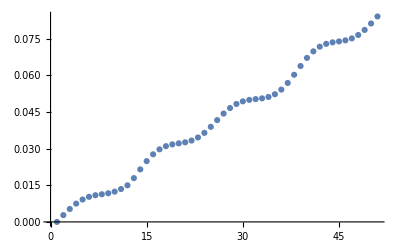

```mathematica
ListPlot[ηsatismaxlist]
```

```mathematica
time = Table[t,{t,0,50}];
```

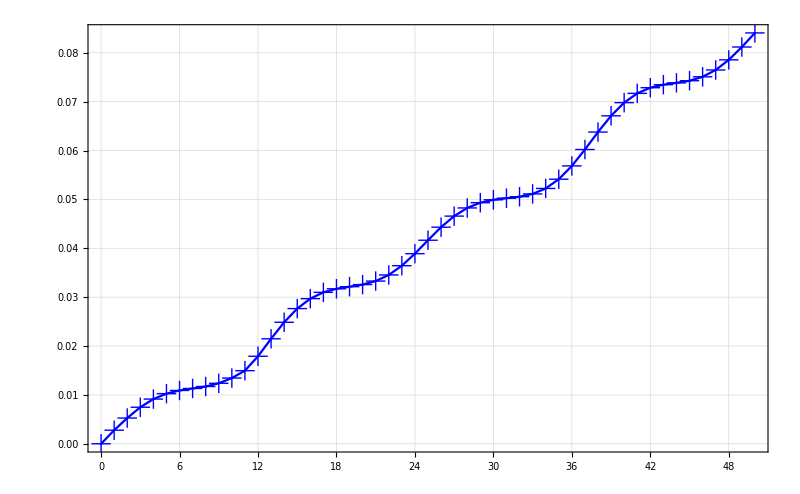

```mathematica
Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

```mathematica
(*Running with Newton-Raphson correction step*)
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤25, i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.00332 seconds.

CPU time consumed: 0.003312 seconds.

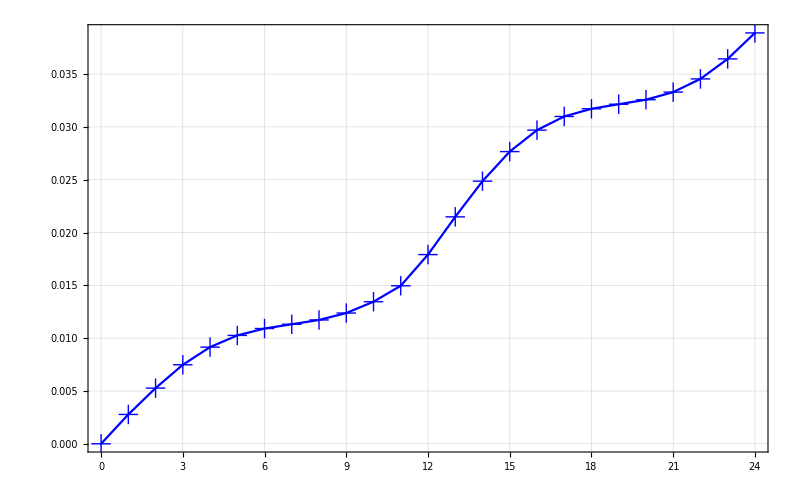

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, 25}];
time = Table[t,{t,0,24}];
part1 = Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

```mathematica
ϕlist[[-1]]
```

{-0.187357,0.0165679,1.31098,-0.202164,0.00238766,-0.0462001,-0.26865,-0.388128,0.25708,0.169234,-0.342867,-0.265931,0.375186,0.319539,-0.0919485,-0.00146148,-0.26136,-0.290132}

```mathematica
legvals[[26]]
```

{1.34637,1.25246,1.18188,1.44743,1.64353,1.49902}

```mathematica
corrϕ = NRTracking[legvals[[25]], ϕlist[[-1]], cηext, cJηext];
```

```mathematica
prevtheta = legvals[[25]];
testext = corrϕ;
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=26,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.0035 seconds.

CPU time consumed: 0.003532 seconds.

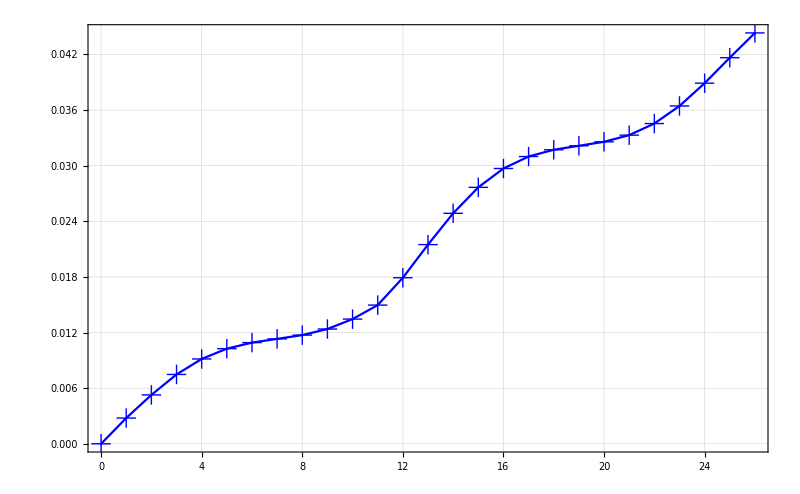

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, 27}];
time = Table[t,{t,0,26}];
part2 = Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

```mathematica
(*Nearest neighbour method*)
```

```mathematica
(*This is will NR solver integrated with NN*)
```

To be done:
1. Find a method in C++ that can couple with the RT to find FK when RT fails

```mathematica
(*Lets come back to Nearest Neighbour later, start documenting the time and updating the C++ codes*)
```

```mathematica
replist=Union[{Power-> pow},{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]} ];
```

```mathematica
cformη = ηext/.Inner[Rule, Join[ϕ, ψ],  Join[p, s], List]/.replist//CForm;
```

```mathematica
(*Porting functions to CPP*)
```

```mathematica
Flatten[Jηext/.Inner[Rule, Join[ϕ, ψ],  Join[p, s], List]/.replist]//CForm;
```

```mathematica
(*Making the DMTracker work in CPP*)
```

```mathematica
prevtheta = legvals[[1]];
DMTracking[thetai_, phii_, Jetatheta_, Jetaphi_] :=  Module[{phinew},
(*Takes in eta and Jeta as compiled functions*)
phinew = phii+(-Inverse[Jetaphi@@Join[phii, thetai]].Jetatheta@@Join[phii, thetai]).(thetai-prevtheta);
prevtheta = thetai;
Return[phinew];
]
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.009406 seconds.

CPU time consumed: 0.008553 seconds.

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tempϕ = testext;
tempϕ = DMTracking[legvals[[2]], tempϕ, cJηextθ, cJηextϕ]
```

{0.199507,0.0262086,1.28199,0.199208,0.0243569,0.0497101,-0.0116145,-0.0999271,0.435303,0.559946,-0.0485772,0.0188021,0.283879,0.274431,-0.00721925,0.0404957,-0.409418,-0.441967}

```mathematica
(*Plotting the with and without NRstep data*)
```

```mathematica
(*With NR step*)
```

```mathematica
tempNRstep = Import["/home/nightmareforev/git/root_tracking/CPP/DMTracker_NR.txt","Table"];
ϕNRstep = Transpose[tempNRstep];
```

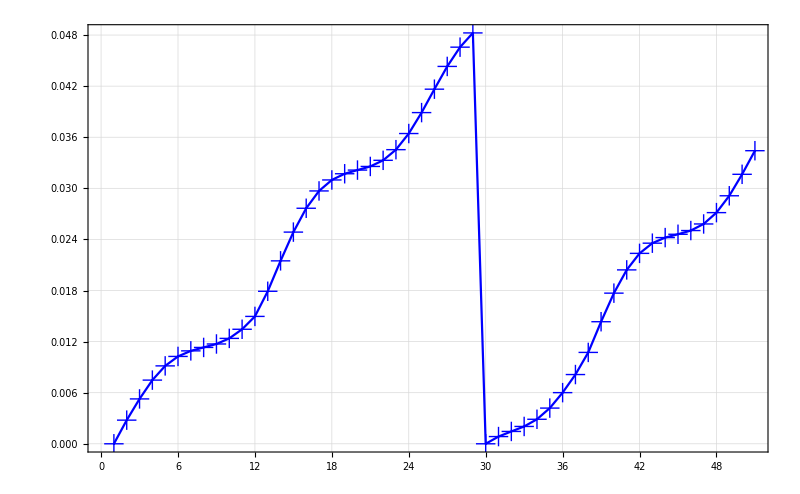

```mathematica
ηsatislistNR = Table[Max[cηext@@Join[ϕNRstep[[i]], legvals[[i]]]],{i, 1, Length[ϕNRstep]}];
time = Table[t,{t,1,Length[ϕNRstep]}];
part2 = Texplot[time, ηsatislistNR, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

```mathematica
tempnoNRstep = Import["/home/nightmareforev/git/root_tracking/CPP/DMTracker_noNR.txt","Table"];
ϕnoNRstep = Transpose[tempnoNRstep];
```

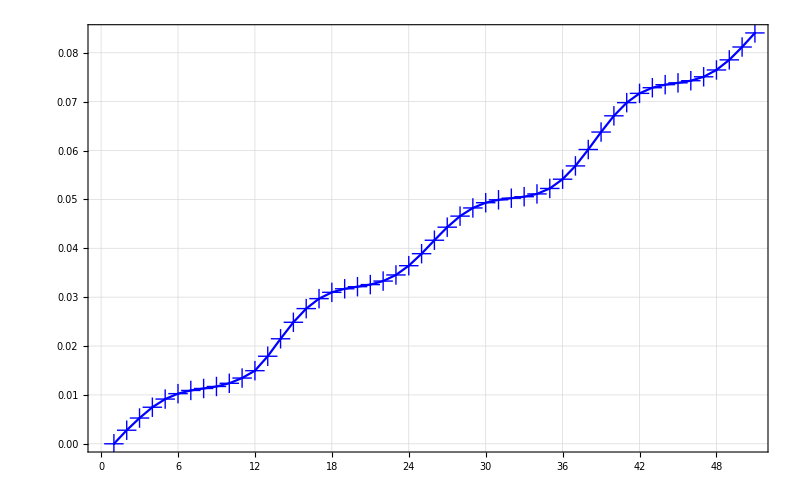

```mathematica
ηsatislistnoNR = Table[Max[cηext@@Join[ϕnoNRstep[[i]], legvals[[i]]]],{i, 1, Length[ϕnoNRstep]}];
time = Table[t,{t,1,Length[ϕnoNRstep]}];
part2 = Texplot[time,ηsatislistnoNR, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

```mathematica
threshold=  Table[0.05,{i, Length[ηsatislistnoNR]}];
```

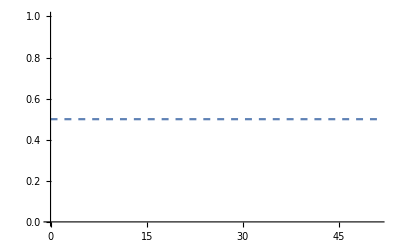

```mathematica
Plot[0.5, {x, 0, Length[ηsatislistnoNR]}, PlotStyle->Dashed]
```

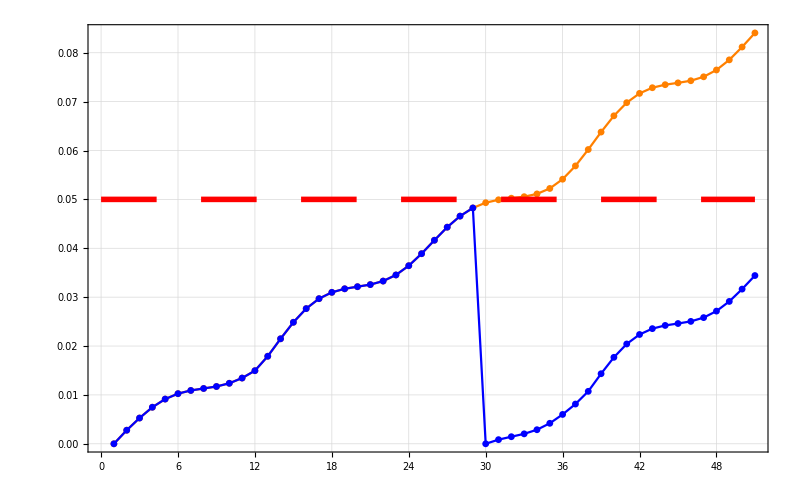

```mathematica
Show[ListPlot[ηsatislistnoNR, PlotStyle->Orange, Joined->True, PlotMarkers->{Automatic, 7}, PlotLegends->Placed[{"Without NR step"},{{Center, 0.95}}]],ListPlot[ηsatislistNR, PlotStyle->Blue, Joined->True, PlotMarkers->{Automatic, 7}, PlotLegends->Placed[{"With NR step"}, {{Center, 0.95}}]], Plot[0.05, {x, 0, Length[ηsatislistnoNR]}, PlotStyle->{Thickness[0.005], Red, Dashing[{0.05, 0.04}]}, PlotLegends->Placed[{"Preset tolerance bound"}, {{Center, 0.95}}]], PlotRange->All, BaseStyle->{FontFamily->"Latin Modern Roman"}, Frame->True,FrameStyle->{Directive[Black,20],Directive[Black,20]}, GridLines->Automatic,PlotStyle->{Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]},PlotMarkers->{"+",20}, FrameLabel->{MaTeX[ToString["\\text{"<>"Discretisation step"<>"}"],Magnification->2],MaTeX[ToString["\\text{Error}~(e_1)"],Magnification->2]},Joined->True, ImageSize->800]
```

```mathematica
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```